# Stats Practice and Data Analysis I

## Lab Ticket

Please do these problems out on a separate sheet of paper and bring them to lab with you.

1. For x_best=20±1 and y_best=40±10, find q_best and its uncertainty for:
	a. q = x+y
	b. q = y-x
	c. q = x*y
	d. q = x/y
Be sure to calculate write your answers with the appropriate number of significant figures.

2. If you measure two independent values as x_best=6.0±0.1 and y_best=3.0±0.1 and use these values to calculate w=xy+x^2/y, what will be your answer and its uncertainty?

## 1. Checking error propagation with Gaussian errors

Many of the measurement distributions we encounter in physics have a Gaussian distribution. Here we will simulate the effect of propagation of Gaussian, or normal, errors. First we will create two Gaussian distributed data sets for the variables x and y. Then we will use them in various functions and observe the shape of the output distribution. This will verify our error propagation techniques and help us understand the conditions under which they are valid.

1. Look up the NormalDistribution, RandomVariate, and Histogram functions. Look in particular at the basic examples in the RandomVariate documentation.

```mathematica
?NormalDistribution
```

NormalDistribution[μ,σ] represents a normal (Gaussian) distribution with mean μ and standard deviation σ.
NormalDistribution[] represents a normal distribution with zero mean and unit standard deviation.

```mathematica
?RandomVariate
```

RandomVariate[dist] gives a pseudorandom variate from the symbolic distribution dist.
RandomVariate[dist,n] gives a list of n pseudorandom variates from the symbolic distribution dist.
RandomVariate[dist,{n_1,n_2,…}] gives an n_1× n_2×… array of pseudorandom variates from the symbolic distribution dist.

```mathematica
?Histogram
```

Histogram[{x_1,x_2,…}] plots a histogram of the values x_i.
Histogram[{x_1,x_2,…},bspec] plots a histogram with bin width specification bspec.
Histogram[{x_1,x_2,…},bspec,hspec] plots a histogram with bin heights computed according to the specification hspec.
Histogram[{data_1,data_2,…},…] plots histograms for multiple datasets data_i.

2. The following function called "list" takes in a mean, standard deviation, and number of samples and outputs a list of values randomly sampled from that distribution. Use the Histogram function to check the output to make sure the Values function does what you think it should.

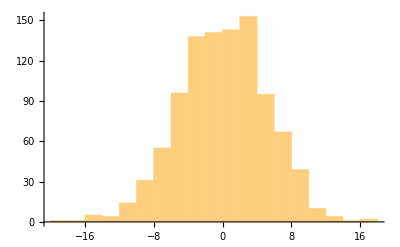

```mathematica
list[mean_,stddev_,n_]:=RandomVariate[NormalDistribution[mean,stddev],n];
Histogram[list[0,5,1000]]
```

This histogram is close to the normal curve, as expected.

3. Using the List function, create two lists, each with 10000 samples: datax and datay. The list datax should be sampled from a distribution with a mean of 20 and a standard deviation of 1. The list datay should be sampled from a distribution with a mean of 40 and a standard deviation of 10. Again, use the Histogram function to check the output to make sure the datax and datay distributions are what you expect them to be.

{19.2498,18.4864,19.684,21.8447,20.6361,20.5816,22.19,20.5905,19.4815,20.1341,19.2987,20.0126,19.0224,9974,21.4596,17.5949,20.2299,19.9571,18.7911,22.0015,20.6862,20.2406,19.1564,19.1888,20.1236,19.7258,20.3466}
 |  |  |  |

{44.9179,39.4497,54.4287,37.2706,40.236,54.8508,37.1214,40.2597,38.8639,34.7354,34.1224,38.965,62.8017,59.253,9972,41.4268,31.294,43.4074,49.7638,47.8877,46.6289,20.8897,46.6201,31.437,31.7346,38.657,63.338,41.7036,33.5162}
 |  |  |  |

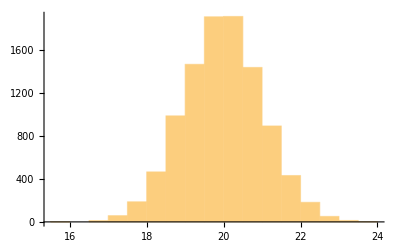

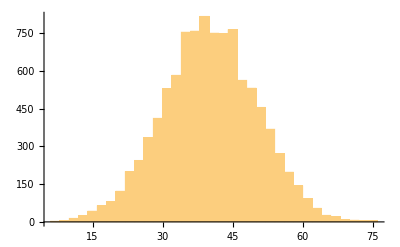

```mathematica
datax = list[20, 1, 10000]
datay = list[40,10,10000]
Histogram[datax]
Histogram[datay]
```

Both of these histograms show a normal curve, with the mean and standard deviations as expected.

4. Create histograms of the following lists: datax+datay, datay-datax, datax*datay, and datax/datay. Do these look like you expect? Compare these to your lab ticket results. Recall the assumptions we made in class about statistical error propagation. Given those assumptions, can you change a single standard deviation and make the non-Gaussian result look more Gaussian? If you'd like, play with more combinations of functions and standard deviations to develop your intuition for when error propagation works.

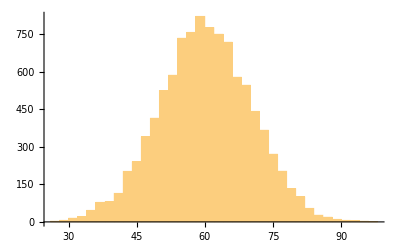

```mathematica
Histogram[datax + datay]
```

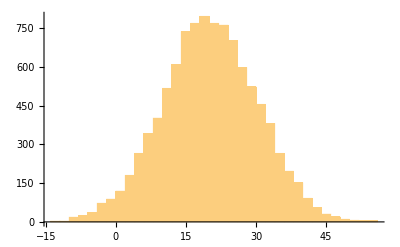

```mathematica
Histogram[datay-datax]
```

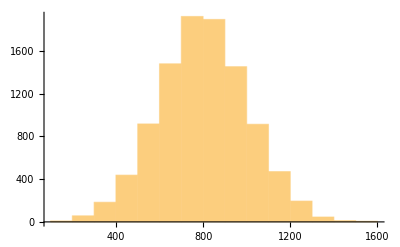

```mathematica
Histogram[datax*datay]
```

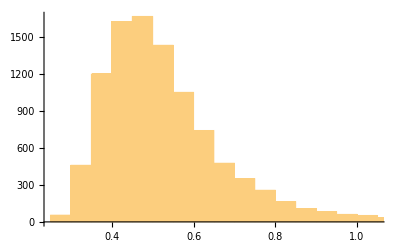

```mathematica
Histogram[datax/datay]
```

The first three results are also normal Gaussian distributions, with means and standard deviations similar to the ones predicted on the lab ticket. However, the division result is skewed to the left, with the mean and standard deviation as predicted, but also with a long right tail. It would be possible to make this look more Gaussian by decreasing the standard deviation on listy, since low outliers in listy are the reason for the long tail.

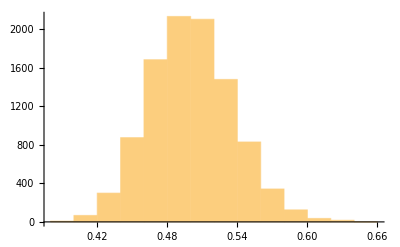

```mathematica
Histogram[datax/list[40,2,10000]]
```

## 2. Checking error propagation with derivatives

Here we’ll work through the steps to have Mathematica take care of the derivatives for error propagation. As with any new tool, you should always check your results against a standard - in this case, your lab ticket.

1. Write a function named “w” that outputs the result given “x” and “y” inputs, based on the formula from problem 2 of your lab ticket.

```mathematica
w[x_,y_] := x y + x^2/y
```

2. Use Mathematica's "D" function to evaluate the two needed partial derivatives for w. Assign these derivatives to new functions using the following syntax: dwdx[x_,y_] = D[w[x,y],x]. [Note the use of '=' (Set) instead of '.=' (Delayed Set). This is crucial, else variable values will get passed later on all the way through the derivative and not allow the derivative to be taken with respect to a set value.] Are these derivatives consistent with what you calculated in your lab ticket?

```mathematica
dwdx[x_,y_] = D[w[x,y],x]
dwdy[x_,y_] = D[w[x,y],y]
```

(2 x)/y+y

x-x^2/y^2

These derivatives match what I had on the lab ticket.

3. Finally, use the dwdx and dwdy functions to calculate the statistical error of w and compare it to your lab ticket.

```mathematica
Sqrt[(dwdx[6.0,3.0] 0.1)^2 + (dwdy[6.0,3.0] 0.1)^2]
```

0.728011

This standard deviation (once significant figures are accounted for) matches the one on the lab ticket.

# 3. Millikan Oil Drop Data Analysis

My answers to these questions are down in the data entry section below.

First we’ll perform two preparation steps, using Mathematica to do the ugly derivatives associated with the error propagation.

-1. Write a function named “q” that outputs the charge given the six parameters required: “d”, “P”, “eta0”, “V”, “v1”, “v2”, based upon the formula from the lab manual.

0. Use Mathematica's "D" function to evaluate the six needed partial derivatives for q. Assign these derivatives to new functions using the following syntax: dqdP[d_, P_, eta0_, V_, v1_, v2_] = D[q[d, P, eta0, V, v1, v2], P].  [Note the use of '=' (Set) instead of '.=' (Delayed Set). This is crucial, else variable values will get passed later on all the way through the derivative and not allow the derivative to be taken with respect to a set value.]

1. Read through the data entry section below. It provides an example of how you will want to enter your data into Mathematica for the experimental labs. Pay some attention to "droptimes" and "risetimes" which are both lists of lists.

2. The viscosity, "eta0", is required, but not yet computed. Add two lines to the Data Entry section to compute "eta0" and "deta0" based on the formula from the lab manual and error propagation.

3. Convert the droptimes and risetimes into velocities for the first drop. Use the Mean function to find the mean value of the dropping velocity and rising velocity. (Think about whether the mean should be taken before or after conversion to velocity.)

4. Now, create a For loop to repeat the process above for each drop. This saves much typing, or at least much copy-and-pasting. The tradeoff is having to think about the indexing of your lists a bit, but it's worth it! Aim for a six-element list "v1" with the falling velocities for each drop and the same for "v2" and rising velocities. 

5. Create a function, "FindQ", that finds the charge on each drop, given as input a falling velocity and a rising velocity. (This is different from the function "q" in that it only inputs the falling and rising velocity, not any other variables.)

6. Run FindQ on your average rising and falling velocities for each drop. Are the charges comparable to that of an electron?

7. Now for the error propagation! First, we need errors on the v1 and v2 values for each drop. Compute the dv1 and dv2 errors (perhaps using the StandardDeviation function).

8. There are errors associated with d, V, eta0, and P as well as with the falling and rising velocities. We have the partial derivatives required for the propagation of errors from step 0. Now we can feed these functions our measured values of d, P, eta0 and V that are the same for all cases, and input the different v1 and v2 for different drops. Using these functions, the velocities for the first drop, and the errors on all measured quantities, compute the error contributions from each of the six variables for the first drop (should be 10^-3 to 10^-1 times charges). What sources of error are most important?

9. Try to automate applying the above process to different drops. Then compute the total error in each drop by adding in quadrature each of the individual errors associated with that drop.

10. Finally, make a plot of charge versus drop number using an ErrorListPlot. First you will need to load the ErrorBar Plotting Package using:

```mathematica
Needs["ErrorBarPlots`"]
```

10. Have a look at your plot. Would this be strong enough data to rule in charge quantization? Using the known value of e, estimate the number of charges on each drop. 

11. For a nice visual on if the charges and their errors are consistent with known multiples of e, let’s overplot horizontal lines corresponding to integer multiples of e on our error bar plot. (a) Make sure you’ve stored your first plot as a variable, for instance chargeplot = ErrorListPlot[....]. (b) Create a second plot with horizontal lines corresponding to multiples of e using something like lineplot = Plot[{a list of relevant multiples of e},{j,1,6}] (Think: why does this produce horizontal lines?) (c) Combine the plots using Show[chargeplot,lineplot].

## Data Entry

The density of the oil is (in kg/m^3).

```mathematica
rho = 886;
```

The value of b that corrects the viscosity of air (in mm Hg * m)

```mathematica
b = 6.17*10^(-6);
```

The temperature in the chamber (in Kelvin) is

```mathematica
T = 293.15 + 24;
```

with error

```mathematica
dT = 1;
```

The voltage between the plates (and error) in Volts is

```mathematica
V = 380;
dV = 0.5;
```

The distance between the plates (in meters) and its error is

```mathematica
d = 7.65*10^(-3);
dd = .1*10^(-3);
```

The room pressure and error (in mm Hg) is

```mathematica
P = 72.5;
dP = .5;
```

Here we create a list of lists of drop times and rise times. All are in seconds. Creating a list of lists like this will make it easy for us to make a for loop that applies the same analysis to each of our drops.

```mathematica
droptimes=Table[0.,{j,1,6}];
risetimes=Table[0.,{j,1,6}];
```

```mathematica
droptimes[[1]] = {15.54, 16.22};
droptimes[[2]] = {9.87, 9.27};
droptimes[[3]] = {10.87, 11.6, 12.75,11.22,12.17};
droptimes[[4]] = {16.12, 14.54, 14.99};
droptimes[[5]] = {14.3, 12.7};
droptimes[[6]] = {7.55, 8.32, 8.88};

risetimes[[1]] = {4.54, 4.92};
risetimes[[2]] = {4.09, 4.38};
risetimes[[3]] = {3.59, 3.22, 2.44,2.54,3.01};
risetimes[[4]] =  {3.32, 3.11, 3.61};
risetimes[[5]] =  {5.85, 5.45};
risetimes[[6]] =  {3.1, 3.78, 3.84};
```

The distance that the drop travels in each of these times is

```mathematica
dist = .5*10^(-3);
```

The acceleration due to gravity at the surface of the earth is (in m/s^2)

```mathematica
g= 9.80665;
```

The accepted charge of the electron (in Coulombs) is

```mathematica
e = 1.602*10^(-19);
```

#### Answers to Part 3 Questions

1.

```mathematica
q[d_,P_,eta0_,V_,v1_,v2_] := 
(4 Pi d rho g)/(3 V) * 
((v1 + v2)/v1) *
(
Sqrt[ (9 eta0 v1)/(2 rho g) + (b^2/(4 P^2))]
- (b/(2P))
)^3
```

```mathematica
q[1,1,1,1,1,1]
q[5,5,5,5,5,5]
```

0.857598

107.242

0.

```mathematica
dqdd[ad_,aP_,aeta0_,aV_,av1_,av2_]       = D[q[ad,aP,aeta0,aV,av1,av2], ad];
dqdP[ad_,aP_,aeta0_,aV_,av1_,av2_]       = D[q[ad,aP,aeta0,aV,av1,av2], aP];
dqdeta0[ad_,aP_,aeta0_,aV_,av1_,av2_]= D[q[ad,aP,aeta0,aV,av1,av2], aeta0];
dqdV[ad_,aP_,aeta0_,aV_,av1_,av2_]       = D[q[ad,aP,aeta0,aV,av1,av2], aV];
dqdv1[ad_,aP_,aeta0_,aV_,av1_,av2_]     = D[q[ad,aP,aeta0,aV,av1,av2], av1];
dqdv2[ad_,aP_,aeta0_,aV_,av1_,av2_]     = D[q[ad,aP,aeta0,aV,av1,av2], av2];
```

2. The viscosity, eta0, and its uncertainty are given by

```mathematica
eta0[T_] := (1.8000 + 0.0048(T-288))*10^-5
deta0[dT_] := Abs[D[eta0[abcd], abcd]] * dT
```

3.

```mathematica
dropvel1 = dist/droptimes[[1]]
Mean[dropvel1]
```

{0.000032175,0.0000308261}

0.0000315006

```mathematica
risevel1 = dist/risetimes[[1]]
Mean[risevel1]
```

{0.000110132,0.000101626}

0.000105879

4.

```mathematica
v1 = Table[0., {j, 1, 6}];
v2 = Table[0., {j, 1, 6}];
```

```mathematica
For[j=1, j<7, j++,
v1[[j]] = Mean[dist/droptimes[[j]] ];
v2[[j]] = Mean[dist/risetimes[[j]] ];
]
```

5.

```mathematica
v1
```

{0.0000315006,0.000052298,0.000042793,0.0000329203,0.0000371676,0.0000608759}

```mathematica
v2
```

{0.000105879,0.000118202,0.000172487,0.000149959,0.0000886066,0.000141258}

```mathematica
FindQ[v1_,v2_] := q[d,P,eta0[T],V, v1, v2]
```

```mathematica
FindQ[1,1]
```

1.47387×10^-12

6.

```mathematica
For[k=1,k<7,k++,
Print[FindQ[v1[[k]],v2[[k]]]]
]
```

4.53537×10^-19

7.6298×10^-19

8.55428×10^-19

6.20255×10^-19

4.59205×10^-19

9.88533×10^-19

The charge of an electron is -1.602*10^-19 C, so these charges are very good.

7.

```mathematica
dv1 = Table[0.,{j,1,6}];
dv2 = Table[0.,{j,1,6}];
```

```mathematica
For[j=1,j<7,j++,
dv1[[j]] = StandardDeviation[dist/droptimes[[j]]];
dv2[[j]] = StandardDeviation[dist/risetimes[[j]]];
]
```

8.

```mathematica
δd = dqdd[d,P,eta0[T],V, v1[[1]],v2[[1]]]* dd
```

5.92859×10^-21

```mathematica
δP = dqdP[d,P,eta0[T],V, v1[[1]],v2[[1]]] * dP
```

7.07724×10^-22

```mathematica
δe = dqdeta0[d,P,eta0[T],V, v1[[1]],v2[[1]]]*deta0[dT]
```

1.81026×10^-21

```mathematica
δV = dqdV[d,P,eta0[T],V, v1[[1]],v2[[1]]] * dV
```

-5.96759×10^-22

```mathematica
δv1 = dqdv1[d,P,eta0[T],V, v1[[1]],v2[[1]]] * dv1[[1]]
```

1.15688×10^-20

```mathematica
δv2 = dqdv2[d,P,eta0[T],V, v1[[1]],v2[[1]]] * dv2[[1]]
```

1.98567×10^-20

The smallest error is due to the temperature, and the velocity, pressure, and distance measurements have relatively large error contributions. The overall error is

```mathematica
dq = N[Sqrt[δd^2 + δP^2 + δe^2 + δV^2 + δv1 + δv2^2]]
```

1.07558×10^-10

9.

```mathematica
totalerrors = Table[0.,{j,1,6}];
For[j=1,j<7,j++,
Module[{δd,δP,δe,δV,δv1,δv2, δq},
δd = dqdd[d,P,eta0[T],V, v1[[1]],v2[[1]]]* dd;
δP = dqdP[d,P,eta0[T],V, v1[[1]],v2[[1]]] * dP;
δe = dqdeta0[d,P,eta0[T],V, v1[[1]],v2[[1]]]*deta0[dT];
δV = dqdV[d,P,eta0[T],V, v1[[1]],v2[[1]]] * dV;
δv1 = dqdv1[d,P,eta0[T],V, v1[[1]],v2[[1]]] * dv1[[1]];
δv2 = dqdv2[d,P,eta0[T],V, v1[[1]],v2[[1]]] * dv2[[1]];
δv2 = dqdv2[d,P,eta0[T],V, v1[[1]],v2[[1]]] * dv2[[1]];
δq = Sqrt[δd^2 + δP^2 + δe^2 + δV^2 + δv1^2 + δv2^2];
totalerrors[[j]] = {FindQ[v1[[j]],v2[[j]]],δq};
Print["Errors for drop ", j, ":"];
Print["δd=",δd];
Print["δP=",δP];
Print["δV=",δV];
Print["δv1=",δv1];
Print["δv2=",δv2];
Print["δq=",δq];
]]
```

Errors for drop 1:

δd=5.92859×10^-21

δP=7.07724×10^-22

δV=-5.96759×10^-22

δv1=1.15688×10^-20

δv2=1.98567×10^-20

δq=2.38204×10^-20

Errors for drop 2:

δd=5.92859×10^-21

δP=7.07724×10^-22

δV=-5.96759×10^-22

δv1=1.15688×10^-20

δv2=1.98567×10^-20

δq=2.38204×10^-20

Errors for drop 3:

δd=5.92859×10^-21

δP=7.07724×10^-22

δV=-5.96759×10^-22

δv1=1.15688×10^-20

δv2=1.98567×10^-20

δq=2.38204×10^-20

Errors for drop 4:

δd=5.92859×10^-21

δP=7.07724×10^-22

δV=-5.96759×10^-22

δv1=1.15688×10^-20

δv2=1.98567×10^-20

δq=2.38204×10^-20

Errors for drop 5:

δd=5.92859×10^-21

δP=7.07724×10^-22

δV=-5.96759×10^-22

δv1=1.15688×10^-20

δv2=1.98567×10^-20

δq=2.38204×10^-20

Errors for drop 6:

δd=5.92859×10^-21

δP=7.07724×10^-22

δV=-5.96759×10^-22

δv1=1.15688×10^-20

δv2=1.98567×10^-20

δq=2.38204×10^-20

10.

```mathematica
Needs["ErrorBarPlots`"]
```

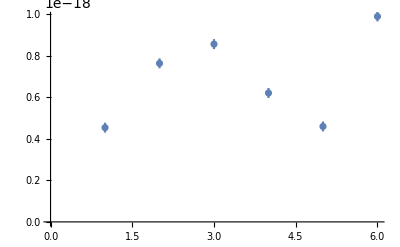

```mathematica
chargeplot = ErrorListPlot[totalerrors]
```

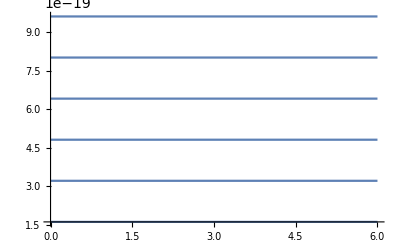

```mathematica
lineplot = Plot[Table[n e, {n, 1, 6}], {j, 0, 6}]
```

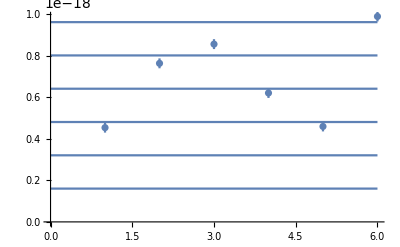

```mathematica
Show[chargeplot,lineplot]
```

This shows that there are drops with 3, 4, 5, and 6 electrons removed.

## 4. Random errors become Gaussian (optional)

Here we will simulate the effect of multiple small random errors on a measurement. Specifically, we’re aiming to show how such accumulated errors result in a Gaussian distribution. Let’s suppose we have measured a value X for the quantity of interest and there are n sources of small random errors. To simplify, let’s assume that each of these n sources has the same magnitude of error, ‘b’.

Each source of error will move the determined value either -b or +b away from the true value. The contribution from all n of these sources will be the sum of n such moves. We can test what the resulting probability distribution should look like by simulating many instances of these moves and seeing what the frequency plot of the results looks like. For even moderate values of n, the frequency plot resembles a Gaussian distribution.

1. Look up the RandomInteger, Histogram and Sum functions.

```mathematica
?RandomInteger
?Histogram
?Sum
```

RandomInteger[{i_min,i_max}] gives a pseudorandom integer in the range {i_min,i_max}. 
RandomInteger[i_max] gives a pseudorandom integer in the range {0,…,i_max}. 
RandomInteger[] pseudorandomly gives 0 or 1. 
RandomInteger[range,n] gives a list of n pseudorandom integers. 
RandomInteger[range,{n_1,n_2,…}] gives an n_1×n_2×… array of pseudorandom integers.

Histogram[{x_1,x_2,…}] plots a histogram of the values x_i.
Histogram[{x_1,x_2,…},bspec] plots a histogram with bin width specification bspec.
Histogram[{x_1,x_2,…},bspec,hspec] plots a histogram with bin heights computed according to the specification hspec.
Histogram[{data_1,data_2,…},…] plots histograms for multiple datasets data_i.

Sum[f,{i,i_max}] evaluates the sum ∑_(i=1)^i_max f. 
Sum[f,{i,i_min,i_max}] starts with i=i_min. 
Sum[f,{i,i_min,i_max,di}] uses steps di. 
Sum[f,{i,{i_1,i_2,…}}] uses successive values i_1, i_2, ….
Sum[f,{i,i_min,i_max},{j,j_min,j_max},…] evaluates the multiple sum ∑_(i=i_min)^i_max ∑_(j=j_min)^j_max …f. 
Sum[f,i] gives the indefinite sum ∑_i f.

2. Write a function called TotalError that outputs the total error from summing the n random errors of +b or -b. Let the value of n and b be inputs for the function.

```mathematica
TotalError[n_,b_] := Sum[b*RandomInteger[{-1, 1}], {i, n}]
```

3. Using your TotalError function, produce a histogram plot of the frequency of different results for the total error. Using the Table function to create the list, draw a total of 5,000 values, letting b=0.1 and trying n=1,3,5,11,25,125.

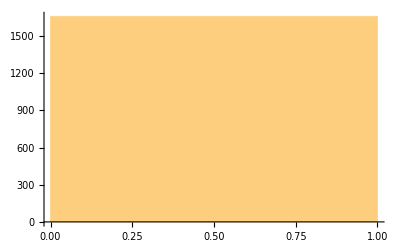

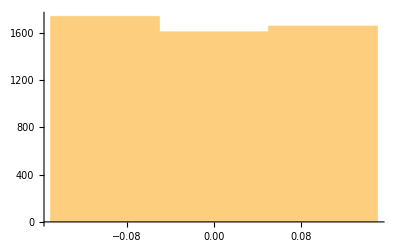

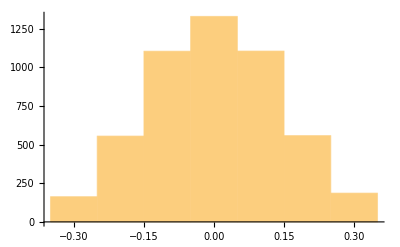

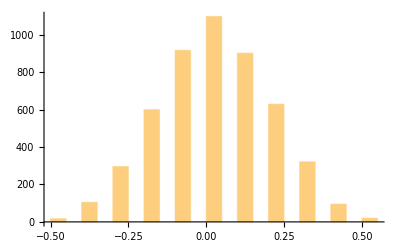

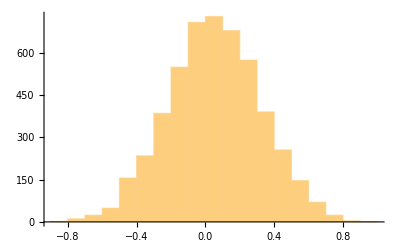

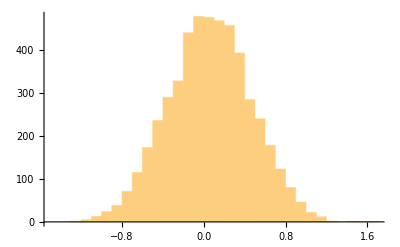

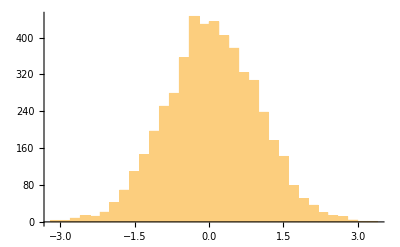

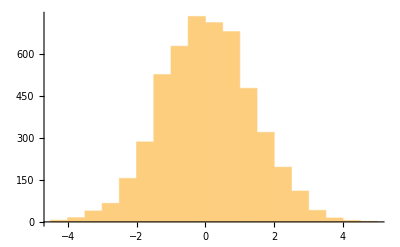

```mathematica
totals = {1,3,5,11,25,125, 250, 1000};

For[i=0,i<Length[totals], i++,
Print[Histogram[Table[TotalError[totals[[i]],0.1], {j, 1, 5000}]]]
]
```

(No need to keep each, but do look through and witness how the shape becomes more and more Gaussian.)
This contribution of many small errors is the essence of why many measured quantities do indeed follow Gaussian distributions.